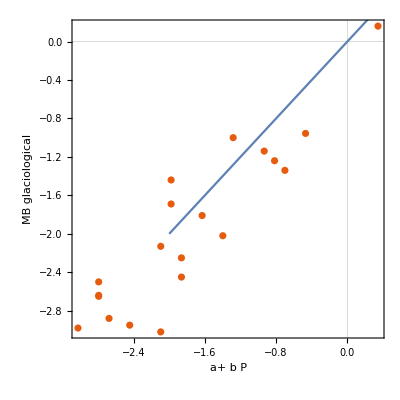
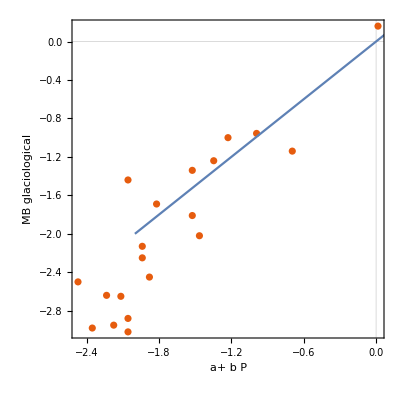
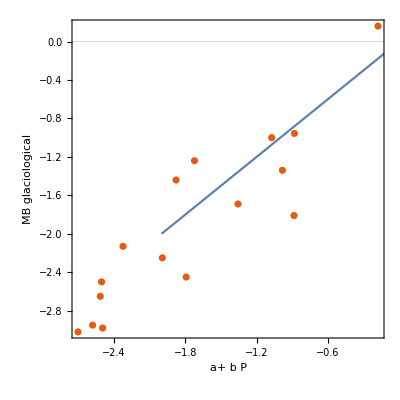
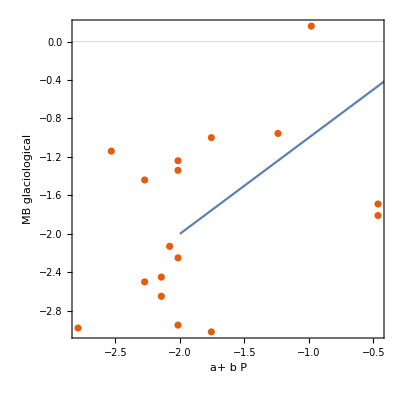
( | Estimate | Standard Error | t-Statistic | P-Value
1 | -1.16617 | 0.316224 | -3.6878 | 0.066301
y | 11.6115 | 6.5959 | 1.76042 | 0.220403 | -Graphics- | 0.9 | 0.42 | -0.18
 | Estimate | Standard Error | t-Statistic | P-Value
1 | -1.70188 | 0.055732 | -30.5368 | 0.00107067
y | 5.92309 | 5.11513 | 1.15795 | 0.366477 | -Graphics- | 0.89 | 0.48 | -0.25
 | Estimate | Standard Error | t-Statistic | P-Value
1 | -5.67735 | 2.49786 | -2.27289 | 0.150938
y | 12.0517 | 7.60083 | 1.58558 | 0.253717 | -Graphics- | 0.9 | 0.41 | -0.15
 | Estimate | Standard Error | t-Statistic | P-Value
1 | 39.1013 | 20.1509 | 1.94043 | 0.191857
y | -0.0129297 | 0.00638293 | -2.02566 | 0.180055 | -Graphics- | 0.4 | 0.84 | -0.03)

```mathematica
(*this file implements the multi proxy algorithm of Banerjee et al., Journal of Glaciology, 2022 for Saint-Sorlin Glacier; details about inputs, algorithm, proxies, and references can  be found in the article and its supplementary material *)
ymsaaann=Transpose@(Import["data_st_sorlin.txt","Table"][[2;;]]);(*importing proxy data; see Supplementary table S5*)
outValErr={ymsaaann[[1]],ymsaaann[[2]]};outputs={};
n0=500; (*Number of noisy runs*)
rows={7,8,6,3}; (*NDSI1, NDSI2, Albedo_MODIS, SLA; See Supplementary table S5; two proxies are ignored due to short length of the records*)
sig={.05,.05,.05,80}; (*Noise level in the proxies*)
For[m=1,m<5,m++, (*Loop over the four proxies*)
geodeticMB=-{1.69,1.78,1.83,1.57}; (*Geodetic data; see Supplementary table S6*)
outMBs={};
For[i=0,i<n0,i++,(*Noisy reconstructions*)
proxy= 1.ymsaaann[[rows[[m]]]];
proxy+=(RandomVariate[NormalDistribution[0,sig[[m]]],Length@proxy]);(*adding noise to the proxy data*)
pMeans=Mean/@{proxy[[1;;15]],proxy[[1;;11]],proxy[[4;;15]],proxy[[1;;9]]};(*proxy mean for the periods*)
p2MB=LinearModelFit[Transpose@{pMeans,geodeticMB+RandomVariate[NormalDistribution[0,.16],Length@geodeticMB]},y,y];(*genrating linear fit after adding noise to the geodeitc data*)
AppendTo[outMBs,Thread@p2MB@proxy];(*best-fit function applied to the annual proxies*)];(*i-loop ends*)
proxy= 1.ymsaaann[[rows[[m]]]];(*repeating for proxy without noise*)
pMeans=Mean/@{proxy[[1;;15]],proxy[[1;;11]],proxy[[4;;15]],proxy[[1;;9]]};
p2MB=LinearModelFit[Transpose@{pMeans,geodeticMB},y,y];
tmp=Select[Transpose@{Thread[p2MB[proxy]],ymsaaann[[2]],proxy},#[[2]]>-999&&#[[3]]>-999&];
AppendTo[outputs,Flatten@{%%,p2MB["ParameterTable"],Show@{ListPlot[Transpose@{tmp[[;;,1]],tmp[[;;,2]]},PlotTheme->"Scientific",PlotRange->All,FrameLabel->{"a+ b P","MB glaciological"},AspectRatio->1],Plot[x,{x,-2,2}]},.01Round@ (100{Correlation[tmp[[;;,1]],tmp[[;;,2]]],Sqrt@Mean@((tmp[[;;,1]]-tmp[[;;,2]])^2),First@Differences@Thread@Mean@tmp})}];(*storing fit details, plots etc*)
Table[AppendTo[outValErr,x],{x,{proxy,Thread[p2MB[proxy]],StandardDeviation@outMBs}}];(*storing numbers*)] (*m-loop ends*)
MatrixForm@outputs
tmp2=Transpose@outValErr;tmp3={};
For[k=1,k≤20,k++,
{m,m2,cnt}={0,0,0};
For[i=3,i<13,i+=3,If[tmp2[[k,i]]>-999,m+=tmp2[[k,i+1]];m2+=(tmp2[[k,i+2]]^2); cnt++];];
AppendTo[tmp3,{m/cnt,Sqrt[m2/(cnt cnt)],cnt}];];
Export["mulprox_outputs_st_sor.txt",Join[tmp2,tmp3,2],"Table"]; (*saving outputs; columns are: Y, b_gla, proxy1, b_rec1,error,proxy2, b_rec2,error,proxy3, b_rec3,error,proxy4, b_rec4,error,b_rec_mul_prox,error, #proxies *)
```